```mathematica
Quit[];
```

```mathematica
h[r_]:=H[r]^-mu(1-(alp r^2)/(2mu (1-4 mu^2))(-H[r]^(2mu+1)+H[r]^2 mu (2mu+1)-4H[r] mu^2+H[r]+mu(2mu -1)));
f[r_]:=H[r]^-mu(1-(alp r^2)/(2mu (1-4 mu^2))(-H[r]^(2mu+1)+H[r]^2 mu (2mu+1)-4H[r] mu^2+H[r]+mu(2mu -1)));
R[r_]:= r H[r]^(1/2(1+mu));
H[r_]:=1 +q/r;
ph[r_]:= Sqrt[1-mu^2] Log[H[r]];
hh=(1-(alp r^2)/(2mu (1-4 mu^2))(-H[r]^(2mu+1)+H[r]^2 mu (2mu+1)-4H[r] mu^2+H[r]+mu(2mu -1)));
```

```mathematica
V[x_]:=-alp/(mu (1-4mu^2))(2Sinh[mu/Sqrt[1-mu^2] x]((2mu^2 +1)Cosh[1/Sqrt[1-mu^2] x]-2mu^2+2)-6mu Sinh[1/Sqrt[1-mu^2] x]Cosh[mu/Sqrt[1-mu^2] x]);
```

```mathematica
SS=Pi R[r]^2;
M=1/2 mu q + (alp q^3)/12;
```

```mathematica
alp=1;
mu=SetPrecision[10/10 ,Infinity];
Clear[q];
Clear[qq];
MM=SetPrecision[5/2,Infinity];
res=Solve[1/2 mu qq + (alp qq^3)/12==MM,qq];
q=N[qq/.res[[1]]];
rPlus=r/. FindRoot[h[r]==0,{r,0.00001,5}];

dTaudr[r_?NumericQ]:=Sqrt[1/(-f[r] )]


tau=NIntegrate[dTaudr[r],{r,1/10^20,rPlus},Method->{"GlobalAdaptive","SingularityDepth"->20},AccuracyGoal->20,PrecisionGoal->20,WorkingPrecision->50];

{mu,tau,MM}
```

NIntegrate::ncvb: 在接近 {r} = {2.5254437612116104286780265811746363041999581183689} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 6.4490629923368474045878473997176162228371723451471 和 0.0050407211442961293488937473776126407475940809327717.

{1,6.4490629923368474045878473997176162228371723451471,5/2}

```mathematica
allData={{-1,21.97836279175771268314322563073691472634784605105100106791452666354690555714554`50.,7},{-9/10,21.89270182605653749977182119243222257937617547001671370398213534599662075184645`50.,7},{-4/5,21.80956888099361677566891334782416195652576084310525876312863845550637215221098`50.,7},{-7/10,21.72891316037137688370203036404579471375542604560641019782670468541066032897958`50.,7},{-3/5,21.65066512002382227958882034989631505892595872059130717771366881078441842796153`50.,7},{-49/100,21.56726038817521815215008291792478762036679149447507210941054724330709688915928`50.,7},{-2/5,21.50098572410350731187414930990964727135919839240673009152647536775003319050429`50.,7},{-3/10,21.4292631396460450474317160332092402014890981668433025069531125384824375051139`50.,7},{-1/5,21.3593437183060773544953710305061345111894875764155513987936280001884591641659`50.,7},{-1/10,21.29093800399006946408830435964153002321881884546756977717712097603412874838387`50.,7},{1/10000,21.22359920921599141476046424138925309828938978891095291543418743157744521944574`50.,7},{1/10,21.1570298530277298705739524575693648855795651408481633085242962365356636784616`50.,7},{1/5,21.09039067397958951737134058726731737476414297836519697315482557438201096468366`50.,7},{3/10,21.02294630508922552842779455593904242922663224334006643764800543492353730295619`50.,7},{2/5,20.95374591812946947422934530372569930443671209413940684933712976425865588016957`50.,7},{49/100,20.8891175549037066420579952329020051373659379123589261026933981659012463425489`50.,7},{3/5,20.80606326217957321497086465669951622358500805741158624681522375014474015211221`50.,7},{7/10,20.72594409838410611710504952311688607822299104859541450204267409321797244909293`50.,7},{4/5,20.6410547053769724002436795536720801302245625624102813177557604862457855826955`50.,7},{9/10,20.55134701883224855344764000820009483385691197255736110327886352508872330711594`50.,7},{1,20.45698235803854478175341873988337646964048179854155466104610587131541264706414`50.,7},{-1,18.83859667785731992138849490171403730114695477503935300813675145433492238220223`50.,6},{-9/10,18.75278006566940477199344161293343792671124996115457941134050882213105844354331`50.,6},{-4/5,18.66954437749366383445995258079891876339922703165005594789187942972787766875701`50.,6},{-7/10,18.58883930118186503049903228939781658248339210886486808503336922687935816915579`50.,6},{-3/5,18.51059602295769219269092368481373960637572876023183402650074622346024716601289`50.,6},{-49/100,18.42726035006528980468937462821639120666730432260276309823222674574231316896406`50.,6},{-2/5,18.36109343130513750513741222192141513798797391858612106096201062138250321114662`50.,6},{-3/10,18.28954695442499698201714093795228796161172767129305800214952921793928990697157`50.,6},{-1/5,18.2198664027919961671885990246980451834075410472960446061709922882156727391605`50.,6},{-1/10,18.15176728455811601020377676291200284994246310259045945267381802679348781756387`50.,6},{1/10000,18.08481206496775352649543911345042582059466549123299193038755715586732009246131`50.,6},{1/10,18.01870572137080591923133630293284681045373604100454429299602549496423033830852`50.,6},{1/5,17.95262854676072672694081770915378113490468925633578424083832026690595833444625`50.,6},{3/10,17.88585875892921883550166011161283837149018868818435726905657209349136420567184`50.,6},{2/5,17.81746482990942545420752384528859049664014993050002842907254481615746712133609`50.,6},{49/100,17.75369385178346542570828061251951399480045063660233798505713879104225900397252`50.,6},{3/5,17.67188665713555891104145439905595922219088933462118991894834476118806396681311`50.,6},{7/10,17.59312514476635404301374428286365577297684531810579711657766603071122457910471`50.,6},{4/5,17.50984214928582914427434332259031631624232731019827516399003212400335169879042`50.,6},{9/10,17.42202216098939609515803738978547247127478133038459478345501933552655363634485`50.,6},{1,17.32985532845225876057651783205295279955524977780573045659762523658668569933243`50.,6},{-1,15.69883056563616139716182955802509972811057894169712470487247767261629341505384`50.,5},{-9/10,15.61280629763504625276497651109597803102251597821988322112766405356084212988398`50.,5},{-4/5,15.52943267923891855986437597119285811955934781791366337586326849258216134932558`50.,5},{-7/10,15.44866030545720749597057775833259347418867946838671748907248117723511790665517`50.,5},{-3/5,15.3704215727487418973551944113384044377403440392938345884189252187763722248855`50.,5},{-49/100,15.28717589399955797579462422116606836885635965239194357462139529525170439794221`50.,5},{-2/5,15.22115100625967047060666681456513383998133374013501169437630039821202987559952`50.,5},{-3/10,15.14983774633101161824833215930282575619792662023551762612134634455903618470326`50.,5},{-1/5,15.08047444095597644705197111687220149106094847868747683869090664247075688722927`50.,5},{-1/10,15.01278329709590396396176589907642517259575741454068138021951410457427891436412`50.,5},{1/10000,14.94633412892815235263390360891965472509288293880930418759752400469806502107958`50.,5},{1/10,14.88085059154592126158098490023307522943282472967898446882936090953415725830036`50.,5},{1/5,14.81552401622213742681630984904176211895756682663204968727019725479359475436499`50.,5},{3/10,14.7496563981205206757364411764489951491288859983509331561845134133742855746446`50.,5},{2/5,14.68234299090269413071220069045557646253117772496429444273234202710121150302954`50.,5},{49/100,14.61972329916129715161197956092021983924355087123318216565037521632208609330179`50.,5},{3/5,14.53959478119805371096447108425635303611951812156479446255239617224326260024873`50.,5},{7/10,14.46266433171751253540140587241970994316981742814324128121359135963935891615394`50.,5},{4/5,14.38155009963705107724806374964698549313697779887219246786544176577427364192068`50.,5},{9/10,14.29627948686261433720015358127476702733458950186011717567039033732117573114549`50.,5},{1,14.20708065932270374486729130235134631169326052730073076958280536916242253244088`50.,5},{-1,12.55906445249524337164203095168691969308701467660971429496723662428466466648564`50.,4},{-9/10,12.47274561099208332774864032510508645264037411616879436848174429333739971342248`50.,4},{-4/5,12.38917439150916005637864746898915126917835880071546657107559965957873717475176`50.,4},{-7/10,12.30830324822363407366745432893183495338131644731072537505337786065485005701247`50.,4},{-3/5,12.2300668027077594787963045247066452355269407490205669618464435948262199052846`50.,4},{-49/100,12.14694376964210792076717450225103876749967593257610233745836930519681210033377`50.,4},{-2/5,12.081116214010563698329234322992916899012194209419352749601083028407307030687`50.,4},{-3/10,12.01012950410965921362514307215388333569178074440105742142677777255134610928428`50.,4},{-1/5,11.94121253607177178165867617079130233412358905648440199558437089987740447713231`50.,4},{-1/10,11.87409725426299210980973851917338840426023663013405192850540602983515910334951`50.,4},{1/10000,11.80836801745018339794499193194659585612686905639411588735886074030781169966311`50.,4},{1/10,11.74376346748457689603603326828884210486223323385115816381456316267228687000087`50.,4},{1/5,11.67950278774845206107970636780104151594906291454762978043301847810053240729811`50.,4},{3/10,11.61491864597083415400498227537053428785523941423544048936576313488417341874427`50.,4},{2/5,11.54914584627417400131983470353464034338039251040797982202406659891679866620655`50.,4},{49/100,11.48817164017750409875357370062309520610157403892814659720719159589864386119369`50.,4},{3/5,11.4104486819182025709808543676379687333011693353002597508968054392978881925649`50.,4},{7/10,11.33614733062814879758205070014019212589354400807318803084292216421083945926398`50.,4},{4/5,11.25814984719149943887544863773028113155635067634845958980054715608322636832682`50.,4},{9/10,11.17654319314095751180111114666483532104092888043923723199725798630085638907423`50.,4},{1,11.09160791453633853624476774239662258977159862574652477209611120135961691683638`50.,4},{-1,9.4161770726769233320084745577822672692477889604651080220672`30.,3},{-9/10,9.3294524991197605918253335772498029002745872106151452082176`30.,3},{-4/5,9.245621136527326920040465389822926511636607955138475196416`30.,3},{-7/10,9.1646397529060670299723490499838714867989693508438554836992`30.,3},{-3/5,9.0864475949717796055452848107264494715242335449325198376959`30.,3},{-49/100,9.003557989205291329029975536117259902424570972273100146591`30.,3},{-2/5,8.9380709219494453642573186068804243501519227362947924754433`30.,3},{-3/10,8.867627594249285409047054949929637810597616376037186207744`30.,3},{-1/5,8.7994372566105463920588561807540211491047638687696440786943`30.,3},{-1/10,8.7332448140444041723769121677884330290275008324905386115072`30.,3},{1/10000,8.67132431675113128865629503062302774812018458211178864253933706842605552213535`50.,3},{1/10,8.6054236182933982737085576829884696032503785454849549664256`30.,3},{1/5,8.5428144591981526709830553701369526127447611888867293003775`30.,3},{3/10,8.480212279917151322952705830266251570228556032166399814724`30.,3},{2/5,8.41683120270472388626397549218708077383691824435136823296`30.,3},{49/100,8.3584445998559477124298563152021197460882872384331135844353`30.,3},{3/5,8.284564518198231149943916873602020360356125792513395151568`30.,3},{7/10,8.2145047189590313817059679639102421549084216659026921914369`30.,3},{4/5,8.141536901659814695088904858733246243185378257196984118975`30.,3},{9/10,8.0658124400964166024927820393570667180905537108618776674304`30.,3},{1,7.9876761480715221867890470025162469096179042356415369838592`30.,3},{-1,7.84941528283836957901254362725756374236072968614371450608468860660440087003557`50.,5/2},{-9/10,7.76229142401910388075698689278538749920667027169420623985023046755232447034162`50.,5/2},{-4/5,7.6781670280666081025252041656958373880533357702081954854202018701298290640429`50.,5/2},{-7/10,7.59700342790532136279354198047002593199857277936271596110136221845592189281036`50.,5/2},{-3/5,7.51874480982270284088554167005607279974648022977538630496941885995431681299311`50.,5/2},{-49/100,7.43592257979178021956716717218829668767553123559834414024078062338193038145223`50.,5/2},{-2/5,7.37060630825166657167227045118701159654358683677039237787432909567158065802976`50.,5/2},{-3/10,7.30048321510856956972282049855049180868440574199674393459075730008787556889241`50.,5/2},{-1/5,7.23276164585752567253153075469900314225777593376579828349688736357446841500399`50.,5/2},{-1/10,7.16720191831488984824370725702619178441934521179797934398500980849975742384389`50.,5/2},{1/10000,7.10342863902003995170919490858952478383740862297232917400059596076610563967765`50.,5/2},{1/10,7.04122620608323833841855302149950622812113916141036377593470005606196115873356`50.,5/2},{1/5,6.97988886568069566745296996527996222516023344315754820617474135448006057347384`50.,5/2},{3/10,6.91883765929116972530294619104253853903147801910365587295533010334646144488001`50.,5/2},{2/5,6.85732123162759616908302928318939236969954327396109105200188665025129976688187`50.,5/2},{49/100,6.80090939627307581149084753035886541834171048864564064940731681163952526218819`50.,5/2},{3/5,6.72987779274791212792581921720141330513570654964840899981369157862310066582061`50.,5/2},{7/10,6.66290351688725071355857298930966578869281004698975040487853950109922868745868`50.,5/2},{4/5,6.59359114941374213436839571167555123468047891302963026373287445561044273844143`50.,5/2},{9/10,6.52217613228921931186519137424836861513723234383297903906231743008588952668201`50.,5/2},{1,6.44906299233684740458784739971761622283717234514710626290566406497543712779946`50.,5/2},{-1,6.27953222627576610909818893109081946247652812548194977770920507277659018652888`50.,2},{-9/10,6.19191495359229460985924057968880953978970336301118385059217656746158025948848`50.,2},{-4/5,6.10744123913561690105087637627398956706138010316758861008507763140399942124132`50.,2},{-7/10,6.0260808495643023631601486817297626280613427213156551004498014092578085924877`50.,2},{-3/5,5.94778666909032271104481955290026967130850159941259650148873790727104076298333`50.,2},{-2/5,5.80009889322075192807058691526567508070351952730712257533395132550839339550382`50.,2},{-49/100,5.8651226381711358306440728562951207380197690415028885509401911929547173939182`50.,2},{-3/10,5.73048451683021686997377734367717827479274391191315552705488841014299367053996`50.,2},{-1/5,5.66347942957540110908865663462325181978766440291153583825918184933038689996343`50.,2},{-1/10,5.5988628553911111239456135535162476378532829263215113576316351080251289908501`50.,2},{1/10000,5.53628547200220810320681365447879645069829419543602585982853630776850911974155`50.,2},{1/10,5.47556056643096485216002662496507174444735787122871839003368481489138573879397`50.,2},{1/5,5.41602990301799361562611511269663944502420248096113821022948245908875789972696`50.,2},{3/10,5.35717006659188658220066969851264564602326880855447719961547205111789374498804`50.,2},{2/5,5.29830146460610441991310691358869608856065607768109097908780147006737622160114`50.,2},{49/100,5.24473390752263653654013202206849856195785730285613342778963429150994685056579`50.,2},{3/5,5.1778785384755541191849644793940416764682035233373065905170874058452296153381`50.,2},{7/10,5.11547380656274105518254988580613418571016666716053249250829559856348857615232`50.,2},{4/5,5.05156177703679314886113638940063182443315550946097646292413148008066126917152`50.,2},{9/10,4.98645165839728352662785235367484119684724373156847539282289480698058863616447`50.,2},{1,4.92060096389280476624623968882322986929547093393328482159792431855160442788458`50.,2},{-1,4.70964916969553222645805388829138510800915691416039932196487865684909206319181`50.,3/2},{-9/10,4.62126115076130799572886210823570216834478141051830958957549681209127852611109`50.,3/2},{-4/5,4.53622534697127241283289673153442223193074241842024033190472817777742142073413`50.,3/2},{-7/10,4.45452947373078493903876645351662509149261704287040483247343976708358554170584`50.,3/2},{-3/5,4.3761447969851726857267630005732520798459208573080713507617084434288904020472`50.,3/2},{-49/100,4.2936870582617449925150860956128033110103631056931395944675854641743487349238`50.,3/2},{-2/5,4.2290888983289954968684609276515916480246298439528848238792825572031161446562`50.,3/2},{-3/10,4.1602401879657604495771123054019139379201195474989783063354358458362167435349`50.,3/2},{-1/5,4.09433473634422277090429503356580596818674764659546947211120268516031662459704`50.,3/2},{-1/10,4.031184107305481126735107938833470619540591878879054688262116148442083849584`50.,3/2},{1/10000,3.97048198306553365905999970391677246689667585256862199442973550737715668176209`50.,3/2},{1/10,3.91208822839082188090764262761693725762907663077198739326013413157138356794974`50.,3/2},{1/5,3.85542008022942803304116604220917856621570351093017505840672155511105318541504`50.,3/2},{3/10,3.80004126322153910202249700436919283758638044485070728376179851174884113921868`50.,3/2},{2/5,3.74538376944546188660585640819000907021400234379861978724589471237741967177606`50.,3/2},{49/100,3.69633908569242068748884868286802909472710373457849636724084411464897127808488`50.,3/2},{3/5,3.6361121555383851540069533999362987245677889069404727117334623527462194073518`50.,3/2},{7/10,3.58092954697328857408196959539974303412030771277430836545311520209700982304784`50.,3/2},{4/5,3.52549727550647603566621130967126334337053240895610384528914977737421970978079`50.,3/2},{9/10,3.47019969958573185700400437712868531367731821688357236091058389554636037731255`50.,3/2},{1,3.41552641743992552309694935111860077515024082029434285658885980770100125297678`50.,3/2},{-1,3.13976611313662937459136809833373021986918496180011455399254477227469054245518`50.,1},{-9/10,3.049973382908693390160864688459282733087055367652697354700842048156732192841`50.,1},{-4/5,2.96385935245358528265240541825487553088925026256295653203458634855997820056964`50.,1},{-7/10,2.88145910042184610666526986749002242190878185757631747468287735781170092333609`50.,1},{-3/5,2.80279356167229958965704520929712703093293875704817588431728786860454842199589`50.,1},{-49/100,2.72057802261100263347489099720386050979024698395958361860376531003322077606097`50.,1},{-2/5,2.6566564530556106738187825321324122770409305602940316710128419571399932653403`50.,1},{-3/10,2.58911934816981768745630036285141264557378639648115883360603576682831945948059`50.,1},{-1/5,2.52517548174191998162567951615513573731189499163126537681654681572654631758898`50.,1},{-1/10,2.46470696465448878496791671343637362930984641260487849480824804676886772154798`50.,1},{1/10000,2.40749421928811961519980740588042088934701785272936279177836684627574698164961`50.,1},{1/10,2.35348593984132595486222056015174061633834797262742658224308072462279997529704`50.,1},{1/5,2.30223647883924488596082047901577121998042703245159196179630080494450037981979`50.,1},{3/10,2.2534609664276126190012749739155351128022058334600416051411792864770960880398`50.,1},{2/5,2.20677782262700280169004709945525204851703750321072131202141936550738596966637`50.,1},{49/100,2.16625382645374948371607510544932173225387235681035026823638472618721998848824`50.,1},{3/5,2.11839379118979444116002122407428493551958587461674460387041581876199944773997`50.,1},{7/10,2.0764852373507815133689101104390978940757831219224563785504618469144214193092`50.,1},{4/5,2.03634039254719355106923974865522693612834872409134840422081534508290852174029`50.,1},{9/10,1.99831438101936212913849106131370996294800475818742254666188689410228686897702`50.,1},{1,1.96276756238382245020850340916399668865500907983560474298097032591032040616177`50.,1}};
```

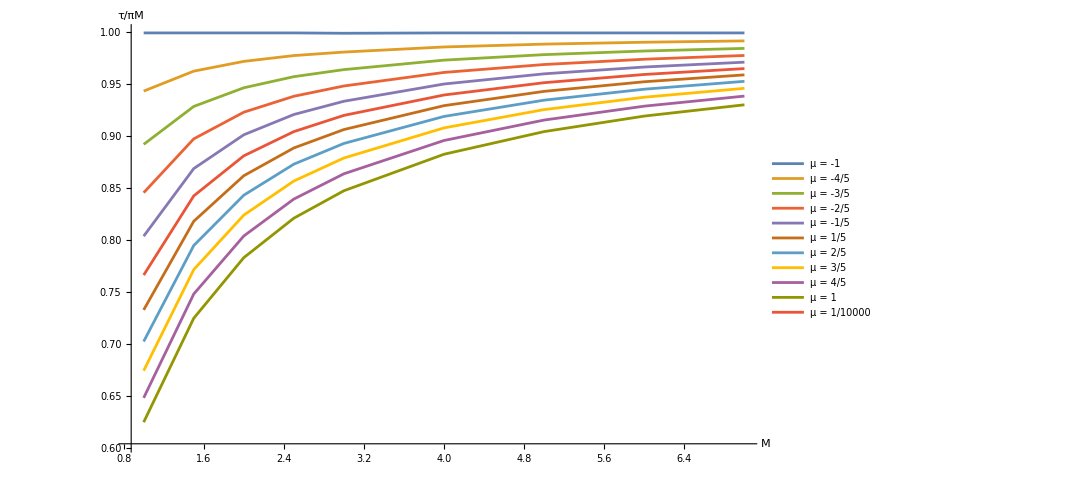

```mathematica
μList=Union[allData[[All,1]]];          
μList=Append[Complement[Range[-1,1,2/10],{0}],1/10000];

NlineMu[μ_]:=Table[{lineMu[μ][[i,1]],lineMu[μ][[i,2]]/(lineMu[μ][[i,1]] π)},{i,Length[lineMu[μ]]}];

nESTL=ListLinePlot[NlineMu/@μList,PlotLegends->Placed[Row/@Thread[{"μ = ",μList}],{0.8,0.5}],Frame->False,AxesLabel->{Style["M",FontSize->16],Style["τ/πM",FontSize->16]},PlotRange->All,ImageSize->800]
```

```mathematica
lineM[i_]:=Select[allData,#[[3]]==i&][[All,{1,2}]]
NlineM[j_]:=Table[{lineM[j][[i,1]],lineM[j][[i,2]]/(lineM[j][[i,1]] π)},{i,Length[lineM[1]]}]
```

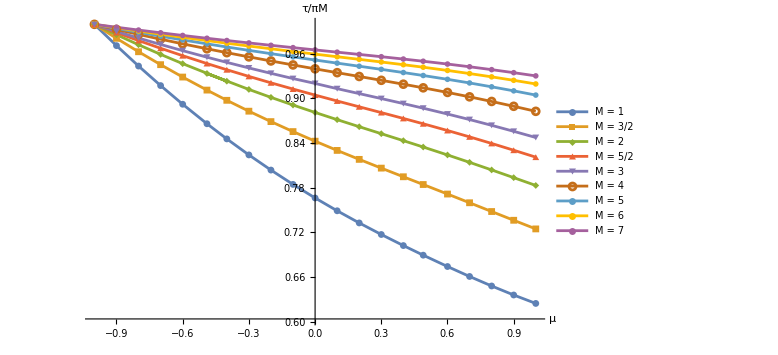

```mathematica
MList=Union[allData[[All,3]]];          

NlineM[M_]:=Table[{lineM[M][[i,1]],lineM[M][[i,2]]/(M π)},{i,Length[lineM[M]]}];

ESPT=ListPlot[NlineM/@MList,PlotLegends->Placed[Row/@Thread[{"M = ",MList}],{0.1,0.35}],Frame->False,Joined->True,PlotMarkers->{Automatic, Small},AxesLabel->{Style["μ",FontSize->16],Style["τ/πM",FontSize->16]},PlotRange->All,ImageSize->Large]
```